```mathematica
ClearAll[a,b,x,y,z,u,v];
a[u_,v_]:=u/3+v
b[u_,v_]:=u/3-2v
x[u_,v_]:=Sin[u]*(7+Cos[u/3-2v]+2Cos[u/3+v])
y[u_,v_]:=Cos[u]*(7+Cos[u/3-2v]+2Cos[u/3+v])
z[u_,v_]:=Sin[u/3-2v]+2Sin[u/3+v]
```

```mathematica
ClearAll[sola, solb];
sola=Solve[a[u,v]==a0,v]
solb=Solve[b[u,v]==b0,v]
```

{{v→1/3 (3 a0-u)}}

{{v→1/6 (-3 b0+u)}}

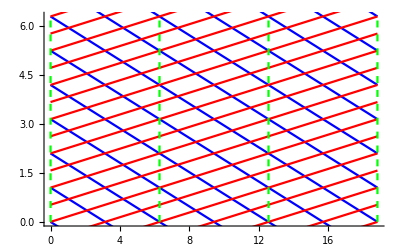

```mathematica
Show[
Table[Plot[v/.sola[[1]],{u,0,6π},PlotStyle->Blue],{a0,-6π,6π,π/3}],
Table[Plot[v/.solb[[1]],{u,0,6π},PlotStyle->Red],{b0,-6π,6π,π/3}],
Table[ParametricPlot[{x0,u},{u,0,2π},PlotStyle->{Dashed,Green}],{x0,0,6π,2π}],
PlotRange->{{0,6π},{0,2π}}]
```

```mathematica
Show[
Table[Plot[v/.sola[[1]],{u,0,6π},PlotStyle->Blue],{a0,-6π,6π,π/3}],
Table[Plot[v/.solb[[1]],{u,0,6π},PlotStyle->Red],{b0,-6π,6π,π/3}],
Table[ParametricPlot[{x0,u},{u,0,2π},PlotStyle->{Dashed,Green}],{x0,0,6π,2π}],
PlotRange->{{0,6π},{0,2π}}]
```

```mathematica
solb[[1]]
```

{v→1/6 (-3 b0+u)}

```mathematica
Show[Table[ParametricPlot3D[{x[u,#],y[u,#],z[u,#]}&[1/3 (3 a0-u)],{u,0,2π},PlotStyle->Blue],{a0,-6π,6π,π/6}],
Table[ParametricPlot3D[{x[u,#],y[u,#],z[u,#]}&[1/6 (-3 b0+u)],{u,0,2π},PlotStyle->Red],{b0,-6π,6π,π/6}],
PlotRange->All]
```

-Graphics3D-